## pixel-based

## fitting

```mathematica
dotSize=21;
dotPoints=Flatten[Table[Table[
If[
EuclideanDistance[{0,0},{i,j}]<dotSize/2,
{i,j},
Nothing
]
,{j,Floor[-dotSize/2],Ceiling[dotSize/2]}],{i,Floor[-dotSize/2],Ceiling[dotSize/2]}],1];
```

```mathematica
dotRatio=0.5;
```

```mathematica
res=Parallelize[Table[
Module[
{image,posList,fillingRatio,fitParam},
image=ConstantArray[0,Round[{dotSize/dotRatio,29 dotSize/dotRatio}]];
posList=Table[{
RandomInteger[Dimensions[image][[1]]],
RandomInteger[Dimensions[image][[2]]]
},{n,1,900}];
fillingRatio=Table[{
n,
N[Length[Select[
DeleteDuplicates[Flatten[Table[Map[pos+#&,dotPoints],{pos,posList[[1;;n]]}],1]],
Between[#[[1]],{1,Dimensions[image][[1]]}]&&
Between[#[[2]],{1,Dimensions[image][[2]]}]
&]]/ProductAcross[Dimensions[image]]]
},{n,1,900,25}];
fitParam=Mean[Flatten[Select[Map[a/.Quiet[Solve[2-(1+Exp[-#[[1]]/a])==#[[2]],a]]&,fillingRatio],Length[#]==1&&NumberQ[#[[1]]]&]]];
{dotRatio,fitParam,fillingRatio}
]
,{dotRatio,0.01,0.3,0.01}]];
```

```mathematica
Transpose[Transpose[res][[1;;2]]]
```

```mathematica
res2={{0.01,366790.19269602123},{0.02,92134.60957369041},{0.03,40968.54612267233},{0.04,22983.5072021985},{0.05,14754.07632907185},{0.06,10409.63096097543},{0.06999999999999999,7628.650384802171},{0.07999999999999999,5860.383374359392},{0.09,4648.177576291479},{0.09999999999999999,3750.165478952977},{0.10999999999999999,3102.742002595605},{0.12,2625.281945233505},{0.13,2244.1743172619867},{0.14,1947.6245222709686},{0.15,1678.3407283804747},{0.16,1474.6223038926241},{0.17,1368.4741582805832},{0.18,1197.2520379850935},{0.19,1060.3575085519938},{0.2,949.3647962982409},{0.21000000000000002,886.9589210517737},{0.22000000000000003,798.308859262075},{0.23,742.7023297771328},{0.24000000000000002,669.8682978799892},{0.25,634.8564318152364},{0.26,570.9294656529814},{0.27,532.965323830488},{0.28,503.1846824141916},{0.29000000000000004,499.8546423218291},{0.30000000000000004,435.3128313772401}};
```

```mathematica
res2fit=NonlinearModelFit[res2,a Exp[b Log[x]]+c,{a,b,c,d},x,MaxIterations->100000];
```

```mathematica
ExponentFitFunction[x_]:=36.1809678369143+37.54838351114363/x^1.9948966301731763
```

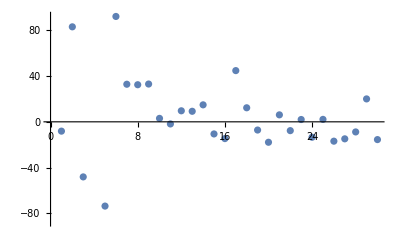

```mathematica
ListPlot[Transpose[Map[
{
#[[1]],
#[[2]],
res2fit[#[[1]]],
#[[2]]-res2fit[#[[1]]]
}
&,res2]][[4]]]
```

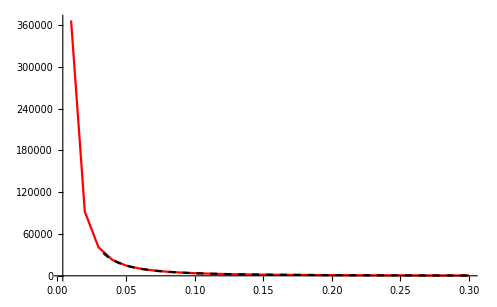

```mathematica
Show[{
ListPlot[res2,Joined->True,PlotRange->All,PlotStyle->Red],
Plot[res2fit[x],{x,0,0.3},PlotStyle->{Dashed,Black}]
}]
```

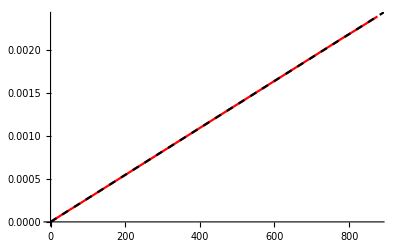

```mathematica
Show[{
ListPlot[
res[[1]][[3]],
Joined->True,PlotRange->{All,All},PlotStyle->Red
],
Plot[
2-(1+Exp[-x/res[[1]][[2]]]),{x,0,900},PlotStyle->{Dashed,Black}
]
}]
```

```mathematica
dotRatio=0.25;
fillingRatio=0.25;
```

```mathematica
HowManyFrames[dotRatio_,fillingRatio_]:=Round[(-37.5484-36.181dotRatio^(1.9948))Log[1-fillingRatio]/dotRatio^(1.9948)]
```

## p5js eval

```mathematica
(HowManyFrames[dotRatio,fillingRatio]-HowManyFrames[dotRatio,0.1])0.9
```

103.5

```mathematica
?Log
```

```mathematica
Log[6]//N
```

1.79176

```mathematica
alma=Round[ImageData[Import[NotebookDirectory[]<>"test.png"]]];
Length[Select[Flatten[alma,1],#=={0,0,0,1}||#=={0,0,0}&]]/Length[Flatten[alma,1]]//N
```

0.252829

```mathematica
(0.28754630948988313+0.15844970076944997)/2
```

0.222998

```mathematica
53
```

```mathematica
HowManyFrames[0.5,0.25]
```

53

```mathematica
0.04547563805104404 0.2521268368136118 0.2521268368136118 9 40 0 49
```

```mathematica
HowManyFrames[0.5,0.04547563805104404]
```

9

```mathematica
HowManyFrames[0.5,0.2521268368136118]
```

54

```mathematica
korte=Round[ImageData[Import[NotebookDirectory[]<>"result.png"]]];
```

```mathematica
korte//Dimensions
```

{1079,1079,4}

```mathematica
Ceiling[1079/29]
```

```mathematica
38
```

```mathematica
N[Length[Position[Flatten[korte[[-38;;-1]],1],{0,0,0,1}]]/(1079 38)]
```

0.243013

```mathematica
N[Length[Position[Flatten[Transpose[Transpose[korte][[-38;;-1]]],1],{0,0,0,1}]]/(1079 38)]
```

0.252085

## do here

```mathematica
dotSize=21;
dotPoints=Flatten[Table[Table[
If[
EuclideanDistance[{0,0},{i,j}]<dotSize/2,
{i,j},
Nothing
]
,{j,Floor[-dotSize/2],Ceiling[dotSize/2]}],{i,Floor[-dotSize/2],Ceiling[dotSize/2]}],1];
```

```mathematica
dotRatio=0.25;
fillingRatio=0.25;
```

```mathematica
image=ConstantArray[0,Round[{dotSize/dotRatio,29 dotSize/dotRatio}]];
```

```mathematica
posList=Table[{
RandomInteger[Dimensions[image][[1]]],
RandomInteger[Dimensions[image][[2]]]
},{n,1,900}];
```

```mathematica
Select[
DeleteDuplicates[Flatten[Table[Map[pos+#&,dotPoints],{pos,posList[[1;;n]]}],1]],
Between[#[[1]],{1,Dimensions[image][[1]]}]&&
Between[#[[2]],{1,Dimensions[image][[2]]}]
&]
```